Galerkin method

```mathematica
Clear["Global`*"]
```

```mathematica
L=4;
```

```mathematica
χ[x_]=1+x;
```

```mathematica
T0[x_]=0;
```

```mathematica
T1[t_]= Sin[ 3 t];
```

```mathematica
E2[t_]= 0;
```

```mathematica
u[x_,t_]= T1[t];
```

```mathematica
sb[x_,t_]= x-D[u[x,t],t]
```

x-3 Cos[3 t]

```mathematica
v[n_,x_]= x^n (1-n/(n+1) x/L)
```

x^n (1-(n x)/(4 (1+n)))

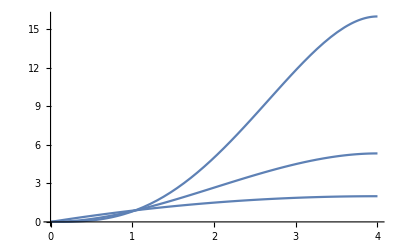

```mathematica
Plot[Table[v[n,x],{n,1,3}],{x,0,L}]
```

```mathematica
ip[f_,g_]:= Integrate[f g,{x,0,L}]
```

The error in class was in this step: I had typed ip[v[m,t],sb[x,t]]

```mathematica
s[m_,t_]=ip[v[m,x],sb[x,t]]
```

ConditionalExpression[(2^(3+2 m) (6+4 m-3 (3+m) Cos[3 t]))/((1+m) (2+m) (3+m)),Re[m]>-1]

```mathematica
vmat[m_,n_]= ip[v[m,x],v[n,x]]
```

ConditionalExpression[(2^(3+2 m+2 n) (3+m (4+m)+4 n+3 m n+n^2))/((1+m) (1+n) (1+m+n) (2+m+n) (3+m+n)),Re[m+n]>-1]

```mathematica
Lmat[m_,n_]= ip[v[m,x],χ[x] D[v[n,x],{x,2}]]
```

ConditionalExpression[-(2^(-1+2 m+2 n) n (5 m^3+m^2 (9+5 n)+m (-4+13 n)+2 (-2+n+n^2)))/((1+m) (-1+m+n) (m+n) (1+m+n) (2+m+n)),Re[m+n]>1]

```mathematica
M=10;
```

```mathematica
odes=Table[Sum[vmat[m,n]c[n]'[t],{n,1,M}]==Sum[Lmat[m,n]c[n][t],{n,1,M}]+s[m,t],{m,1,M}];
```

```mathematica
odes[[1]]
```

128/15 c[1]'[t]+832/45 c[2]'[t]+4864/105 c[3]'[t]+13312/105 c[4]'[t]+69632/189 c[5]'[t]+352256/315 c[6]'[t]+1736704/495 c[7]'[t]+(16777216 c[8]'[t])/1485+(79691776 c[9]'[t])/2145+(373293056 c[10]'[t])/3003==4/3 (10-12 Cos[3 t])-14/3 c[1][t]-72/5 c[2][t]-224/5 c[3][t]-15104/105 c[4][t]-3328/7 c[5][t]-11264/7 c[6][t]-249856/45 c[7][t]-3211264/165 c[8][t]-3801088/55 c[9][t]-106430464/429 c[10][t]

```mathematica
icip[m_]= ip[v[m,x],T0[x]-u[x,0]]
```

0

```mathematica
ics=Table[c[n][0]==0,{n,1,M}]
```

{c[1][0]==0,c[2][0]==0,c[3][0]==0,c[4][0]==0,c[5][0]==0,c[6][0]==0,c[7][0]==0,c[8][0]==0,c[9][0]==0,c[10][0]==0}

```mathematica
vars=Table[c[n][t],{n,1,M}]
```

{c[1][t],c[2][t],c[3][t],c[4][t],c[5][t],c[6][t],c[7][t],c[8][t],c[9][t],c[10][t]}

```mathematica
sol=NDSolve[Join[odes,ics],vars,{t,0,8}]
```

{{c[1][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[2][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[3][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[4][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[5][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[6][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[7][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[8][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[9][t]→InterpolatingFunction[{{0., 8.}}, <>][t],c[10][t]→InterpolatingFunction[{{0., 8.}}, <>][t]}}

```mathematica
ΔT[x_,t_]= Sum[c[n][t] v[n,x],{n,1,M}]/.sol[[1]];
```

```mathematica
T[x_,t_]=u[x,t]+ΔT[x,t];
```

```mathematica
T[x,0]
```

0.

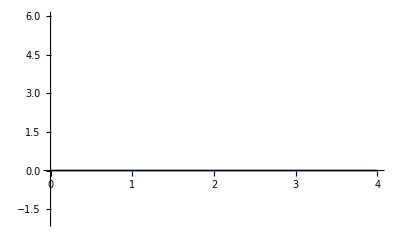
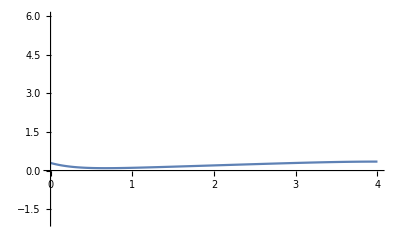
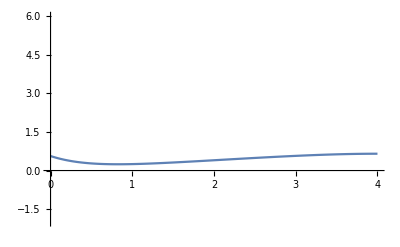
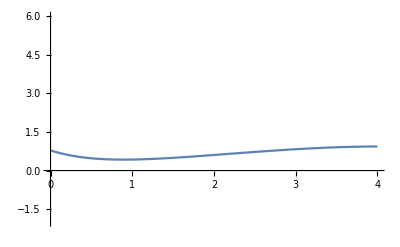
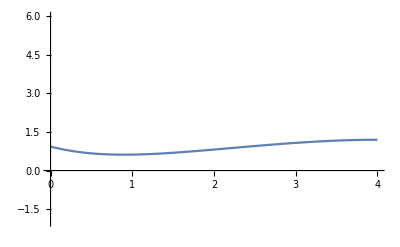
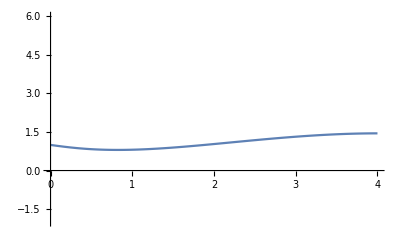
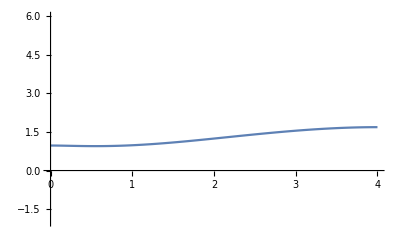
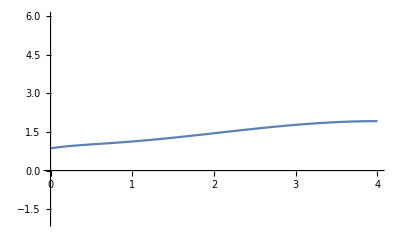

```mathematica
TTab=Table[Plot[T[x,t],{x,0,L},PlotRange->{-2,6}],{t,0,8,.1}]
```

```mathematica
ListAnimate[TTab]
```

Grid Method

```mathematica
Clear["Global`*"]
```

```mathematica
L=4.;
```

```mathematica
M=40;
```

```mathematica
Δx=L/M
```

0.1

```mathematica
x[m_]= m Δx
```

0.1 m

```mathematica
χ=1
```

1

```mathematica
Clear[T]
```

```mathematica
T[n_,m_]:= T[n,m]=T[n-1,m]+Δt χ/Δx^2 (T[n-1,m+1]-2T[n-1,m]+T[n-1,m-1])
```

```mathematica
T[0,m_]= Sin[x[m] Pi/L]
```

Sin[0.0785398 m]

```mathematica
T[n_,0]=0;
T[n_,M]=0;
```

```mathematica
Δt=0.002;
```

```mathematica
T[1,1]
```

0.0783624

```mathematica
Ttab[n_]:=Table[{m Δx,T[n,m]},{m,0,M}]
```

```mathematica
Ttab[1]
```

{{0.,0},{0.1,0.0783624},{0.2,0.156242},{0.3,0.233158},{0.4,0.308636},{0.5,0.382212},{0.6,0.453431},{0.7,0.521854},{0.8,0.58706},{0.9,0.648647},{1.,0.706235},{1.1,0.759468},{1.2,0.808019},{1.3,0.851589},{1.4,0.889908},{1.5,0.92274},{1.6,0.949884},{1.7,0.971171},{1.8,0.98647},{1.9,0.995688},{2.,0.998767},{2.1,0.995688},{2.2,0.98647},{2.3,0.971171},{2.4,0.949884},{2.5,0.92274},{2.6,0.889908},{2.7,0.851589},{2.8,0.808019},{2.9,0.759468},{3.,0.706235},{3.1,0.648647},{3.2,0.58706},{3.3,0.521854},{3.4,0.453431},{3.5,0.382212},{3.6,0.308636},{3.7,0.233158},{3.8,0.156242},{3.9,0.0783624},{4.,0}}

```mathematica
Tfun[n_]:=Tfun[n]= Interpolation[Ttab[n]]
```

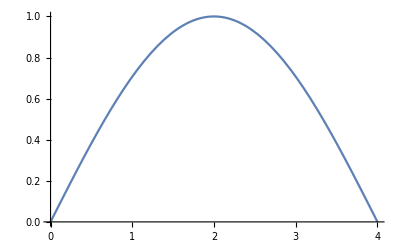

```mathematica
Plot[Tfun[0][x],{x,0,L}]
```

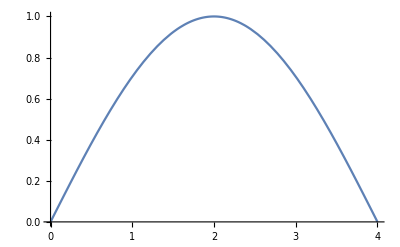
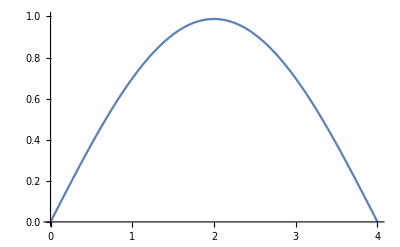
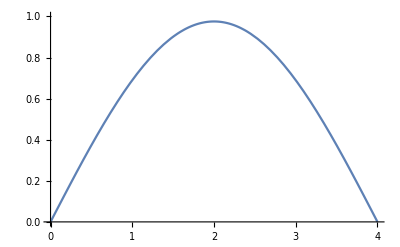
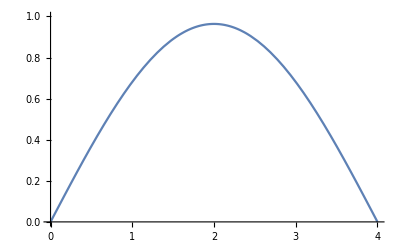
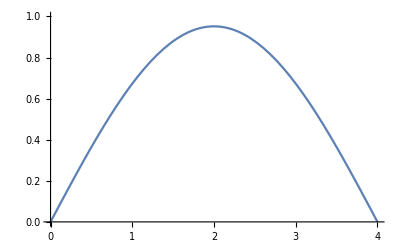
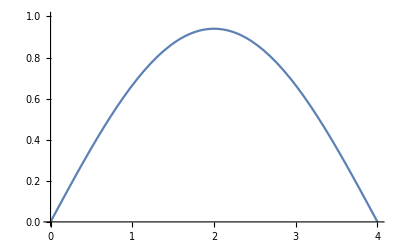
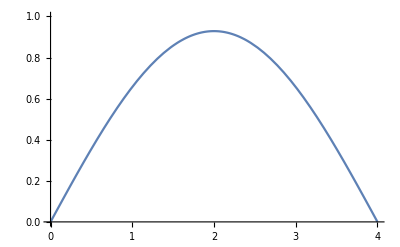
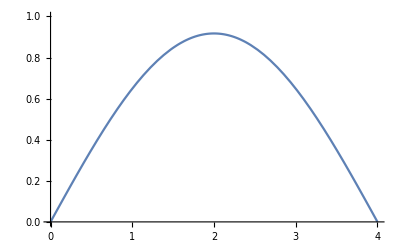
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[Tfun[n][x],{x,0,L},PlotRange->{0,1}],{n,0,500,10}]
```

```mathematica
ListAnimate[%]
```

```mathematica
Clear[T]
```

```mathematica
Δt=0.0053;
```

```mathematica
T[n_,m_]:= T[n,m]=T[n-1,m]+Δt χ/Δx^2 (T[n-1,m+1]-2T[n-1,m]+T[n-1,m-1])
```

```mathematica
T[0,m_]=x[m](L-x[m])
```

0.1 (4.-0.1 m) m

```mathematica
T[n_,0]=0;
T[n_,M]=0;
```

```mathematica
T[1,1]
```

0.3794

```mathematica
Ttab[n_]:=Table[{m Δx,T[n,m]},{m,0,M}]
```

```mathematica
Ttab[1]
```

{{0.,0},{0.1,0.3794},{0.2,0.7494},{0.3,1.0994},{0.4,1.4294},{0.5,1.7394},{0.6,2.0294},{0.7,2.2994},{0.8,2.5494},{0.9,2.7794},{1.,2.9894},{1.1,3.1794},{1.2,3.3494},{1.3,3.4994},{1.4,3.6294},{1.5,3.7394},{1.6,3.8294},{1.7,3.8994},{1.8,3.9494},{1.9,3.9794},{2.,3.9894},{2.1,3.9794},{2.2,3.9494},{2.3,3.8994},{2.4,3.8294},{2.5,3.7394},{2.6,3.6294},{2.7,3.4994},{2.8,3.3494},{2.9,3.1794},{3.,2.9894},{3.1,2.7794},{3.2,2.5494},{3.3,2.2994},{3.4,2.0294},{3.5,1.7394},{3.6,1.4294},{3.7,1.0994},{3.8,0.7494},{3.9,0.3794},{4.,0}}

```mathematica
Clear[Tfun]
```

```mathematica
Tfun[n_]:=Tfun[n]= Interpolation[Ttab[n]]
```

```mathematica
Plot[Tfun[0][x],{x,0,L}]
```

-Graphics-

```mathematica
Table[Plot[Tfun[n][x],{x,0,L},PlotRange->{0,5}],{n,0,100,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[%]
```